# Assignment 2

## Thu Si Nguyen Mai - s4278836

```mathematica
Quit[]
```

## A2-1

```mathematica
f[x_,y_]:=x^3-y^3-3x+3y
plotF=Plot3D[f[x,y], {x, -3, 3}, {y, -3,3}, AxesLabel->{"x","y", "f"},BoxRatios->{1, 1, 1}, ColorFunction->ColorData["Rainbow"]]
```

-Graphics3D-

### Linear approximation

```mathematica
(*point (0,0)*)
(*1st order approximation*)
linA11=Normal[Series[f[x,y],{x,0,1},{y,0,1}]]//Simplify
(*2nd order approximation*)
linA12=Normal[Series[f[x,y],{x,0,2},{y,0,2}]]//Simplify
(*tangent plane is the 1st order approximation*)
plotT1=Plot3D[linA11,{x,-3,3},{y,-3,3},PlotStyle->LightGray];
Show[{plotF, plotT1}, AxesLabel->{"x", "y", "f"},PlotRange->All,BoxRatios->{1,1,1}]
```

-3 x+3 y

-3 x+3 y

-Graphics3D-

```mathematica
(*point (-1,1)*)
(*1st order approximation*)
linA21=Normal[Series[f[x,y],{x,-1,1},{y,1,1}]]//Simplify
(*2nd order approximation*)
linA22=Normal[Series[f[x,y],{x,-1,2},{y,1,2}]]//Simplify
(*tangent plane is the 1st order approximation*)
plotT2=Plot3D[linA21,{x,-3,3},{y,-3,3},PlotStyle->LightGray];
Show[{plotF, plotT2}, AxesLabel->{"x", "y", "f"},PlotRange->All,BoxRatios->{1,1,1}]
```

4

4-3 (1+x)^2-3 (-1+y)^2

-Graphics3D-

### Extrema

```mathematica
(*The 4 extreme values*)
{e1, e2, e3, e4}=Values[Solve[D[f[x,y], x]==0&&D[f[x,y],y]==0, {x,y}]]
```

{{-1,-1},{1,-1},{-1,1},{1,1}}

```mathematica
mH=D[f[x,y],{{x,y},2}];
MatrixForm[mH]
```

(6 x | 0
0 | -6 y)

```mathematica
(*function for evaluating extreme values*)
evalEx[hess_]:= If[Det[hess]>0, If[Tr[hess]<0, "Maximum", "Minimum"], "Saddle point"]
(*1st extreme value*)
mH1=mH/.{x->e1[[1]], y->e1[[2]]};
MatrixForm[mH1]
evalEx[mH1]
```

(-6 | 0
0 | 6)

Saddle point

```mathematica
(*2nd extreme value*)
mH2=mH/.{x->e2[[1]], y->e2[[2]]};
MatrixForm[mH2]
evalEx[mH2]
```

(6 | 0
0 | 6)

Minimum

```mathematica
(*3rd extreme value*)
mH3=mH/.{x->e3[[1]], y->e3[[2]]};
MatrixForm[mH3]
evalEx[mH3]
```

(-6 | 0
0 | -6)

Maximum

```mathematica
(*4th extreme value*)
mH4=mH/.{x->e4[[1]], y->e4[[2]]};
MatrixForm[mH4]
evalEx[mH4]
```

(6 | 0
0 | -6)

Saddle point

### Value of f(x,y) at its single local maximum

```mathematica
f[e3[[1]], e3[[2]]]
```

4

## A2-2

```mathematica
mA={{-1, -3}, {3, -1}};
MatrixForm[mA]
ode={D[x[t],t]==mA[[1,1]]*x[t]+mA[[1,2]]*y[t],
D[y[t],t]==mA[[2,1]]*x[t]+mA[[2,2]]*y[t]}
re1={x[t+1]==mA[[1,1]]*x[t]+mA[[1,2]]*y[t],
y[t+1]==mA[[2,1]]*x[t]+mA[[2,2]]*y[t]}
```

(-1 | -3
3 | -1)

{x'[t]==-x[t]-3 y[t],y'[t]==3 x[t]-y[t]}

{x[1+t]==-x[t]-3 y[t],y[1+t]==3 x[t]-y[t]}

### Study the system of recurrence equations

```mathematica
init={x[0]==1, y[0]==2}
```

{x[0]==1,y[0]==2}

```mathematica
solRe1=RSolveValue[{re1, init}, {x[t],y[t]},t] // ComplexExpand // Simplify
```

{10^(t/2) (Cos[t (π-ArcTan[3])]-2 Sin[t (π-ArcTan[3])]),10^(t/2) (2 Cos[t (π-ArcTan[3])]+Sin[t (π-ArcTan[3])])}

-Graphics-

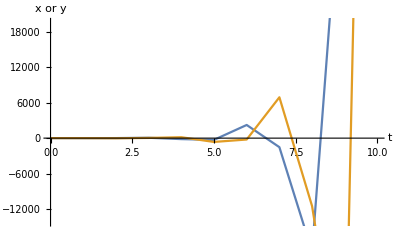

-Graphics-

```mathematica
pt=DiscretePlot[{solRe1[[1]], solRe1[[2]]}, {t, 0,100}, Joined->True, Filling->None,AxesLabel->{"t", "x or y"}]
pt=DiscretePlot[{solRe1[[1]], solRe1[[2]]}, {t, 0,10}, Joined->True, Filling->None, AxesLabel->{"t", "x or y"}]
pt=DiscretePlot[{solRe1[[1]], solRe1[[2]]}, {t, 200,210}, Joined->True, Filling->None, AxesLabel->{"t", "x or y"}]
```

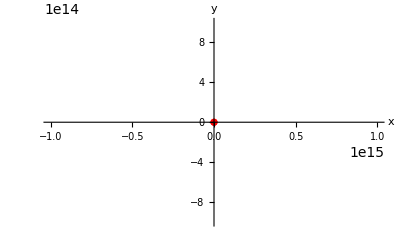

-Graphics-

```mathematica
(*time from 0 to 100*)
xy=Table[{solRe1[[1]]/.t->i, solRe1[[2]]/.t->i},{i, 0, 100}];
pp=ListLinePlot[xy, AxesLabel->{"x", "y"}, PlotRange->Full];
initXY=ListPlot[{xy[[1]]}, PlotStyle->Red]; (*initial point in red*)
Show[pp, initXY]
(*time from 250 to 260*)
xy=Table[{solRe1[[1]]/.t->i, solRe1[[2]]/.t->i},{i, 250, 260}];
pp=ListLinePlot[xy, AxesLabel->{"x", "y"}, PlotRange->Full];
initXY=ListPlot[{xy[[1]]}, PlotStyle->Red]; (*initial point in red*)
Show[pp, initXY]
```

### Study the system of ODEs

```mathematica
solODE=DSolveValue[{ode, init}, {x[t], y[t]}, t]
```

{ⅇ^-t (Cos[3 t]-2 Sin[3 t]),ⅇ^-t (2 Cos[3 t]+Sin[3 t])}

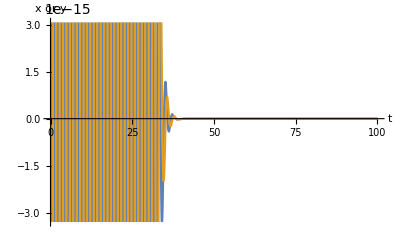

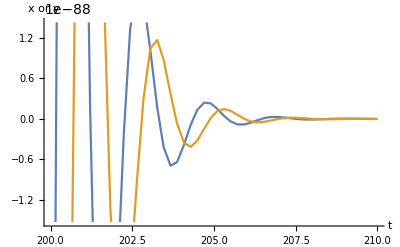

```mathematica
pt=Plot[solODE, {t, 0,100},AxesLabel->{"t", "x or y"}]
pt=Plot[solODE, {t, 200,210},AxesLabel->{"t", "x or y"}]
```

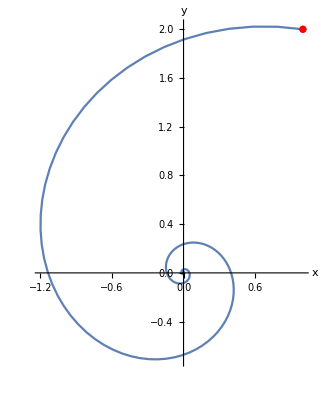

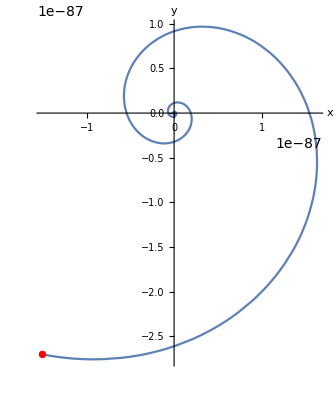

```mathematica
(*time from 0 to 100*)
pp=ParametricPlot[solODE, {t, 0, 100}, AxesLabel->{"x", "y"}];
initXY=ListPlot[{solODE/.t->0}, PlotStyle->Red];(*initial point*)
Show[{pp, initXY}, PlotRange->Full]
(*time from 200 to 210*)
pp=ParametricPlot[solODE, {t, 200, 210}, AxesLabel->{"x", "y"}];
initXY=ListPlot[{solODE/.t->200}, PlotStyle->Red];(*initial point*)
Show[{pp, initXY}, PlotRange->Full]
```

### Compare the 2 systems

```mathematica
lambda=Eigenvalues[mA]
Re[lambda]
modulus=Sqrt[Re[lambda[[1]]]^2 + Im[lambda[[1]]]^2];
N[modulus]
```

{-1+3 ⅈ,-1-3 ⅈ}

{-1,-1}

3.16228

## A2-3

### Study the system of recurrence equation for the special case Δt=1

```mathematica
re2={x[t+1]==x[t]+mA[[1,1]]*x[t]+mA[[1,2]]*y[t],
y[t+1]==y[t]+mA[[2,1]]*x[t]+mA[[2,2]]*y[t]}
init={x[0]==1, y[0]==2}
```

{x[1+t]==-3 y[t],y[1+t]==3 x[t]}

{x[0]==1,y[0]==2}

```mathematica
solRe2=RSolveValue[{re2, init}, {x[t], y[t]},t] //ComplexExpand//Simplify
```

{3^t (Cos[(π t)/2]-2 Sin[(π t)/2]),3^t (2 Cos[(π t)/2]+Sin[(π t)/2])}

```mathematica
pt=DiscretePlot[{solRe2[[1]], solRe2[[2]]}, {t, 0,100}, Joined->True, Filling->None,AxesLabel->{"t", "x or y"}]
```

-Graphics-

```mathematica
xy=Table[{solRe2[[1]]/.t->i, solRe2[[2]]/.t->i},{i, 0, 100}];
pp=ListLinePlot[xy, AxesLabel->{"x", "y"}, PlotRange->Full];
initXY=ListPlot[{xy[[1]]}, PlotStyle->Red]; (*initial point in red*)
Show[pp, initXY]
```

-Graphics-

### For smaller values of Δt

```mathematica
re3[delta_]:={x[t+1]==x[t]+delta*(mA[[1,1]]*x[t]+mA[[1,2]]*y[t]),
y[t+1]==y[t]+delta*(mA[[2,1]]*x[t]+mA[[2,2]]*y[t])}
re3[Δt]
mAre3[delta_]:={{1+delta*mA[[1,1]], delta*mA[[1,2]]}, {delta*mA[[2,1]],1+delta*mA[[2,2]]}}
mAre3[Δt]//MatrixForm
init={x[0]==1, y[0]==2}
```

{x[1+t]==x[t]+Δt (-x[t]-3 y[t]),y[1+t]==Δt (3 x[t]-y[t])+y[t]}

(1-Δt | -3 Δt
3 Δt | 1-Δt)

{x[0]==1,y[0]==2}

```mathematica
solRe3=RSolveValue[{re3[deltaT], init}, {x[t], y[t]},t]
```

{1/2 ((1-2 ⅈ) (1-(1+3 ⅈ) deltaT)^t+(1+2 ⅈ) (1-(1-3 ⅈ) deltaT)^t),1/2 ((2+ⅈ) (1-(1+3 ⅈ) deltaT)^t+(2-ⅈ) (1-(1-3 ⅈ) deltaT)^t)}

```mathematica
time[delta_]:=DiscretePlot[{solRe3[[1]]/.deltaT->delta, solRe3[[2]]/.deltaT->delta}, {t, 0, 50/delta},Joined->True, Filling->None, AxesLabel->{"t", "x or y"}, ImageSize->{400, 400}]
phase[delta_]:=ListLinePlot[Table[{solRe3[[1]]/.deltaT->delta, solRe3[[2]]/.deltaT->delta}, {t, 0, 50/delta}], AxesLabel->{"x", "y"}, PlotRange->All,ImageSize->{400, 400}]
initXYval[delta_]:={solRe3[[1]]/.{deltaT->delta, t->0}, solRe3[[2]]/.{deltaT->delta, t->0}}

Manipulate[{time[par1], initXYval[par1],phase[par1]},{{par1,0.5,"delta t"},0.01,0.5, Appearance->"Labeled"}]
```

```mathematica
(*delta=0.5*)
dt=0.5;
l=Eigenvalues[mAre3[dt]]
Sqrt[Re[l[[1]]]^2 + Im[l[[2]]]^2]
```

{0.5+1.5 ⅈ,0.5-1.5 ⅈ}

1.58114

```mathematica
(*delta=0.3*)
dt=0.3;
l=Eigenvalues[mAre3[dt]]
Sqrt[Re[l[[1]]]^2 + Im[l[[2]]]^2]
```

{0.7+0.9 ⅈ,0.7-0.9 ⅈ}

1.14018

```mathematica
(*delta=0.2*)
dt=0.2;
l=Eigenvalues[mAre3[dt]]
Sqrt[Re[l[[1]]]^2 + Im[l[[2]]]^2]
```

{0.8+0.6 ⅈ,0.8-0.6 ⅈ}

1.

```mathematica
(*delta=0.19*)
dt=0.19;
l=Eigenvalues[mAre3[dt]]
Sqrt[Re[l[[1]]]^2 + Im[l[[2]]]^2]
```

{0.81+0.57 ⅈ,0.81-0.57 ⅈ}

0.990454

```mathematica
(*delta=0.001*)
dt=1/1000;
l=Eigenvalues[mAre3[dt]]
Sqrt[Re[l[[1]]]^2 + Im[l[[2]]]^2]
N[%]
```

{999/1000+(3 ⅈ)/1000,999/1000-(3 ⅈ)/1000}

(3 √(11089/10))/100

0.999005